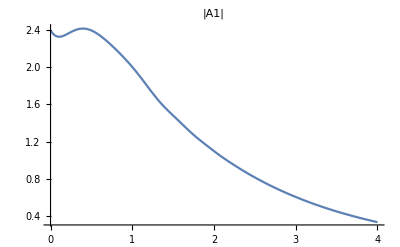

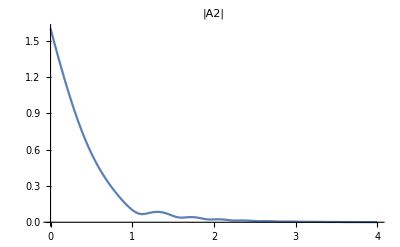

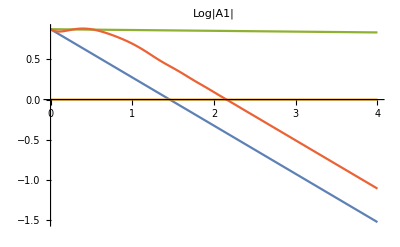

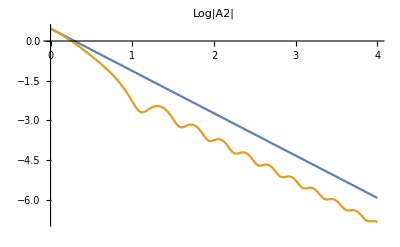

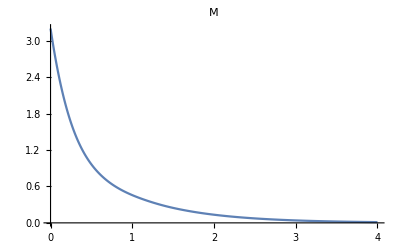

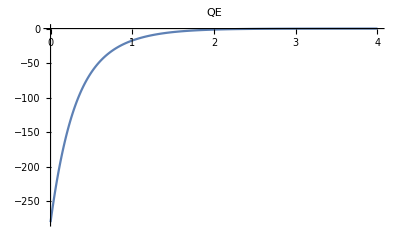

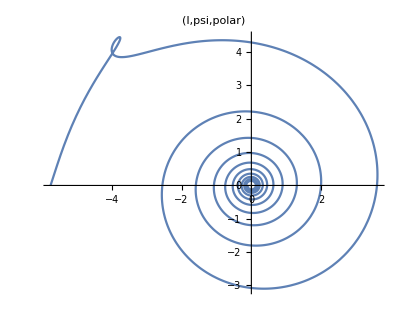

-Graphics3D-

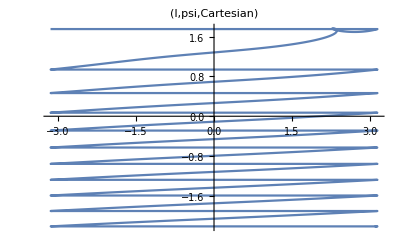

-Graphics3D-

-Graphics3D-

```mathematica
ClearAll[EOM,EOM1n, EOM2n,A1,A2,pv];
g12v=0.3;
g11v=1;
g22v=0;
G1v=.6;
G2v=1.6;
dc1v=1;
 Δω21v=-25; 
(* Δω21v=2 Pi(3 64580 -199599)/G2v; *)
Fv=0;
w1v=1;
pv={g12->g12v,g11->g11v,g22->g22v,G1->G1v,G2->G2v,Δω21->Δω21v,w1->w1v};
EOM=Chop[{EQA1,EQA2}/.pv];
EOM1n=EOM[[1]];
EOM2n=EOM[[2]];
Mn=(Abs[A1[t]]^2/9+ Abs[A2[t]]^2);
Eq3n=Eq3/.pv;

qq=0.8;
A10=qq  3;
A20=-qq 2;
tmax=4;
soln=NDSolve[ {EOM1n==0,EOM2n==0,A1[0]==A10,A2[0]==A20},{A1[t],A2[t]},{t,0,tmax}];
(* ,AccuracyGoal->35,PrecisionGoal->11*)
Plot[Abs[A1[t]]/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"|A1|"]
Plot[Abs[A2[t]]/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"|A2|"]
(* Plot[{Log[Abs[A10]Exp[-G1v t]],Log[Abs[A1[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A1|"]
Plot[{Log[Abs[A20]Exp[-G2v t]],Log[Abs[A2[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A2|"] *)
Plot[{Log[Abs[A10]Exp[-G1v t]],0 Log[Abs[A10]Exp[-(G1v+G2v) t]],Log[Abs[A10]Exp[-(g12v/3g11v)^2 t]],Log[Abs[A1[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A1|"]
Plot[{Log[Abs[A20]Exp[-G2v t]],Log[Abs[A2[t]]]/.soln},{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"Log|A2|"]
Plot[(Mn/.soln),{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"M"]
Plot[(Eq3n/.soln),{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"QE"]
ParametricPlot[{Abs[A1[t]]^2 Cos[3 Arg[A1[t]]-Arg[A2[t]]],Abs[A1[t]]^2 Sin[3 Arg[A1[t]]-Arg[A2[t]]]}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,polar)"]
ParametricPlot3D[{Abs[A1[t]]^2 Cos[3 Arg[A1[t]]-Arg[A2[t]]],Abs[A1[t]]^2 Sin[3 Arg[A1[t]]-Arg[A2[t]]],Mn}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,M, polar)"]
ParametricPlot[{Mod[3 Arg[A1[t]]-Arg[A2[t]],2Pi,-Pi],Log[Abs[A1[t]]^2] }/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,Cartesian)"]
ParametricPlot3D[{Mod[3 Arg[A1[t]]-Arg[A2[t]],2Pi,-Pi],Log[Abs[A1[t]]^2] ,Mn}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,M,Cartesian)"]
ParametricPlot3D[{Abs[A1[t]]^2 Cos[3 Arg[A1[t]]-Arg[A2[t]]],Abs[A1[t]]^2 Sin[3 Arg[A1[t]]-Arg[A2[t]]],Eq3n}/.soln,{t,0,tmax},PlotRange->All,PlotPoints->300,PlotLabel->"(I,psi,QE)"]
```